# LEED

## Loading Stuffs I might need

```mathematica
<<ErrorBarPlots`
```

```mathematica
<<PhysicalConstants`
```

```mathematica
ClearSystemCache[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Helper Functions

### Reading in the data and doing stuff on it

Reads in data from files formatted as filename, whether clicked, x-coordinate, y-coordinate

```mathematica
ClearAll[ReadRawData]
ReadRawData[file_]:=ReadList[file,{Word,Word,Real,Real}]
```

Rearranges the data, trims all non-digits from filename (hope you gave them decend names ;) ), transmogrifies the resulting numbers from strings to real numbers and rescales them (this is optional, if no scaling is given, the scaling defaults to 1). Dito for adding. The two cut parameters were added later, to be able to cut off parts of the filename string after trimming it (the reason were / between numbers in filenames)

```mathematica
ClearAll[SortRawData]
SortRawData[rawdata_,scaling_:1,add_:0,cutf_:0,cutb_:0]:={rawdata⟦All,2⟧,(#+add)&/@(scaling*ToExpression[StringDrop[StringDrop[StringTrim[#,RegularExpression["[^[:digit:]]"]...],cutf],-cutb]]&/@rawdata⟦All,1⟧),rawdata⟦All,3⟧,rawdata⟦All,4⟧}ᵀ
```

deletes all peaks that do not have the value left for clicked, that means all that were rightclicked (i.e. have nlft). Alternatively they can have the value leftleft, which is later on important for the combination of two peaks

```mathematica
ClearAll[KillDeadPeaks]
KillDeadPeaks[almostdata_]:=Delete[almostdata,Position[(First[#]=="left"||First[#]=="leftleft")&/@almostdata,False]]
```

```mathematica
ClearAll[ReadPeakData]
ReadPeakData[file_,scaling_:1,add_:0,cutf_:0,cutb_:0]:=Module[{rawdata,almostdata,justonemorestepdata,data},
rawdata=ReadRawData[file];
almostdata=SortRawData[rawdata,scaling,add,cutf,cutb];
justonemorestepdata=KillDeadPeaks[almostdata];
data=Take[justonemorestepdata,All,{2,4}]
]
```

This function is there to combine data of two peaks

```mathematica
ClearAll[CombinePeaks]
CombinePeaks[{string1_,a_,x1_,y1_},{string2_,b_,x2_,y2_}]:={StringJoin[string1,string2],If[a==b,a,∞],x1-x2,y1-y2}
```

```mathematica
ClearAll[ReadAndCombinePeakData]
ReadAndCombinePeakData[file1_,file2_,scaling_:1,add_:0,cutf_:0,cutb_:0]:=Module[{rawdata1,rawdata2,almostdata1,almostdata2,justonemorestepmommy,data},
rawdata1=ReadRawData[file1];
rawdata2=ReadRawData[file2];
almostdata1=SortRawData[rawdata1,scaling,add,cutf,cutb];
almostdata2=SortRawData[rawdata2,scaling,add,cutf,cutb];
justonemorestepmommy=MapThread[CombinePeaks,{almostdata1,almostdata2}];
data=Take[KillDeadPeaks[justonemorestepmommy],All,{2,4}]
]
```

```mathematica
ClearAll[PeakDistance]
PeakDistance[{energy_,x_,y_},m_,n_]:={12.26/(√energy),1/(√(m^2+n^2))√(x^2+y^2)//N}
```

```mathematica
ClearAll[PeakDistanceMap]
PeakDistanceMap[peakdata_,m_,n_]:=PeakDistance[#,m,n]&/@peakdata
```

Well, we also need to read in the data from the I(V)-curve file...

```mathematica
ClearAll[ReadIVrawData]
ReadIVrawData[file_]:=ReadList[file,{Real,Real,Real,Real,Real,Real,Real}]
```

```mathematica
ClearAll[ReadIVdata]
ReadIVdata[file_]:=Module[{rawdata,almostdata,min,data},
rawdata=ReadIVrawData[file];
almostdata={#⟦1⟧,#⟦3⟧}&/@rawdata;
min=Min[almostdata⟦All,2⟧];
data={#⟦1⟧,#⟦2⟧-min}&/@almostdata
]
```

```mathematica
ClearAll[IvPeakFit]
IvPeakFit[data_,{min_,max_}]:=Module[{region,midpoint,maxheight},
region=Select[data,First[#]≥min&& First[#]≤max&];
midpoint=Round[(min+max)/2];
maxheight=Max[region⟦All,2⟧];
NonlinearModelFit[region,A/(1+((x-a)/b)^2),{{A,maxheight},{a,midpoint},b},x,MaxIterations->1000]
]
```

```mathematica
ClearAll[IvPeakFit2]
IvPeakFit2[data_,{min_,mid_,max_}]:=Module[{region,region1,region2,midpoint1,midpoint2,maxheight1,maxheight2},
region=Select[data,First[#]≥min&& First[#]≤max&];
region1=Select[data,First[#]≥min&& First[#]≤mid&];
region2=Select[data,First[#]≥mid&& First[#]≤max&];
midpoint1=Round[(min+mid)/2];
midpoint2=Round[(mid+max)/2];
maxheight1=Max[region1⟦All,2⟧];
maxheight2=Max[region2⟦All,2⟧];
NonlinearModelFit[region,A1/(1+((x-a1)/b2)^2)+A2/(1+((x-a2)/b2)^2),{{A1,maxheight1},{A2,maxheight2},{a1,midpoint1},{a2,midpoint2},b1,b2},x,MaxIterations->1000]
]
```

### Plotting and shiny stuff

```mathematica
ClearAll[ErrorForm]
ErrorForm[{x_?NumberQ,Δx_?NumberQ},dgts_:2]:=ToString[PaddedForm[N[Round[x,10^(-dgts)]],{dgts+2,dgts}]]<>" ±"<>ToString[PaddedForm[N[Ceiling[Abs[Δx],10^(-dgts)]],{dgts+1,dgts}]]
```

```mathematica
niceStyle={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Dashed,Gray]
};
```

ClearAll[PeakFitPlot]
PeakFitPlot[data_, fit_] := Show[ListPlot[data], Plot[Normal[fit], {x, Min[First[#] & /@ data], Max[First[#] & /@ data]}], niceStyle]

```mathematica
ClearAll[PeakFitPlot]
PeakFitPlot[data_,fit_,title_:"",bottom_:"Electron Wavelength [Å]",left_:"weighted Peak-to-Peak distance [px]"]:=Show[ListPlot[data,PlotLabel->Style[title,16],FrameLabel->{StyleForm[bottom,FontSize->14],StyleForm[left,FontSize->14]}],Plot[Normal[fit],{x,Min[First[#]&/@data],Max[First[#]&/@data]}],niceStyle]
```

```mathematica
ClearAll[GroupPeakFitPlot]
GroupPeakFitPlot[data_,fits_,title_:"",bottom_:"",left_:""]:=Show[ListPlot[data,PlotLabel->Style[title,16],FrameLabel->{StyleForm[bottom,FontSize->14],StyleForm[left,FontSize->14]}],Plot[Evaluate[Normal[#]&/@fits],{x,Min[First[#]&/@(Join@@data)],Max[First[#]&/@(Join@@data)]}],niceStyle]
```

## Import Data

### Calibration Data

calibfiles = FileNames[{"*.bmp"}, FileNameJoin[{"calib"}]];

calib = Import[#] & /@ calibfiles;

```mathematica
(calibdata=ReadPeakData["data/calib.txt",0.1])//TableForm;
```

### Lateral

```mathematica
(peak10=PeakDistanceMap[ReadAndCombinePeakData["data/p1_p0.txt","data/m1_p0.txt",1,49,2,0],1,0])//TableForm;
```

```mathematica
(peak11a=PeakDistanceMap[ReadAndCombinePeakData["data/p1_p1.txt","data/m1_m1.txt",1,49,2,0],1,1])//TableForm;
```

```mathematica
(peak11b=PeakDistanceMap[ReadAndCombinePeakData["data/p1_m1.txt","data/m1_p1.txt",1,49,2,0],1,1])//TableForm;
```

```mathematica
(peak01=PeakDistanceMap[ReadAndCombinePeakData["data/p0_p1.txt","data/p0_m1.txt",1,49,2,0],0,1])//TableForm;
```

```mathematica
(peak20=PeakDistanceMap[ReadAndCombinePeakData["data/p2_p0.txt","data/m2_p0.txt",1,49,2,0],2,0])//TableForm;
```

```mathematica
(peak02=PeakDistanceMap[ReadAndCombinePeakData["data/p0_p2.txt","data/p0_m2.txt",1,49,2,0],0,2])//TableForm;
```

```mathematica
(peak21a=PeakDistanceMap[ReadAndCombinePeakData["data/p2_p1.txt","data/m2_m1.txt",1,49,2,0],2,1])//TableForm;
```

```mathematica
(peak21b=PeakDistanceMap[ReadAndCombinePeakData["data/p2_m1.txt","data/m2_p1.txt",1,49,2,0],2,1])//TableForm;
```

```mathematica
(peak12a=PeakDistanceMap[ReadAndCombinePeakData["data/p1_p2.txt","data/m1_m2.txt",1,49,2,0],1,2])//TableForm;
```

```mathematica
(peak12b=PeakDistanceMap[ReadAndCombinePeakData["data/p1_m2.txt","data/m1_p2.txt",1,49,2,0],1,2])//TableForm;
```

```mathematica
(peak22b=PeakDistanceMap[ReadAndCombinePeakData["data/p2_m2.txt","data/m2_p2.txt",1,49,2,0],2,2])//TableForm;
```

### Perpendicular

```mathematica
(ivdata=ReadIVdata["data/curve.txt"])//TableForm;
```

## Evaluation

### Calibration

```mathematica
calibfit1=NonlinearModelFit[Take[calibdata,All,{1,2}],m*(x-a)Degree+n,{m,a,n},x]
```

FittedModel[2400.34-9.44516 (-12.9692+x)]

```mathematica
calibfit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | -541.168 | 11.3544 | -47.6614 | 5.7187×10^-9
a | 12.9692 | 4.63282 | 2.79943 | 0.0311875
n | 2400.34 | 0.490497 | 4893.69 | 4.91454×10^-21

```mathematica
calibfit2=NonlinearModelFit[Take[calibdata,All,{1,2}],A*Sin[(2*x-a)Degree]+c,{A,a,c},x]
```

FittedModel[283.182-282.919 Sin[° (-114.656+2 x)]]

```mathematica
calibfit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | -282.919 | 16.6759 | -16.9657 | 2.68128×10^-6
a | 114.656 | 17.4568 | 6.56797 | 0.000597048
c | 283.182 | 80.9742 | 3.49719 | 0.0128703

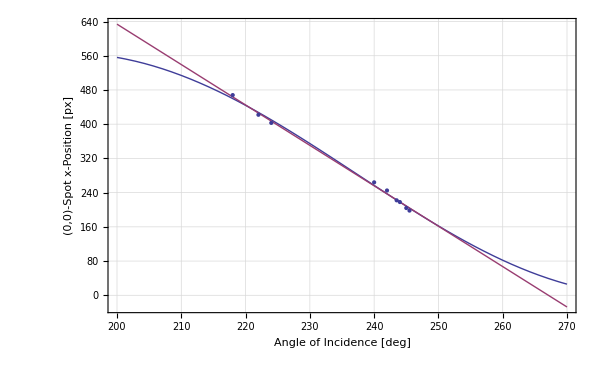

```mathematica
Show[Plot[{Normal[calibfit2],Normal[calibfit1]},{x,200,270},FrameLabel->{StyleForm["Angle of Incidence [deg]",FontSize->14],StyleForm["(0,0)-Spot x-Position [px]",FontSize->14]}],ListPlot[Take[calibdata,All,{1,2}]],niceStyle]
```

```mathematica
error=10;
```

```mathematica
calibfit3=NonlinearModelFit[Take[calibdata,All,{1,2}],A*Sin[(2*x-a)Degree]+c,{A,a,c},x,
Weights->Table[1/error^2,{i,1,Length[calibdata]}],
VarianceEstimatorFunction->(1&)]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[283.182-282.919 Sin[° (-114.656+2 x)]]

```mathematica
calibfit3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | -282.919 | 23.3033 | -12.1407 | 0.0000189812
a | 114.656 | 24.3945 | 4.70007 | 0.00332593
c | 283.182 | 113.155 | 2.5026 | 0.0463647

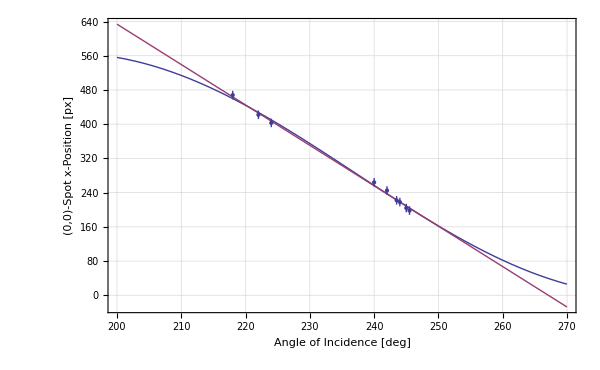

```mathematica
Show[Plot[{Normal[calibfit2],Normal[calibfit1]},{x,200,270},FrameLabel->{StyleForm["Angle of Incidence [deg]",FontSize->14],StyleForm["(0,0)-Spot x-Position [px]",FontSize->14]}],ErrorListPlot[Join[Take[calibdata,All,{1,2}]ᵀ,{Table[error,{i,1,Length[calibdata]}]}]ᵀ],niceStyle]
```

### Lateral Lattice Constant

#### Linear Fit

```mathematica
allpeaks=Select[#,First[#]>0&]&/@{peak10,peak11a,peak11b,peak01,peak20,peak02,peak21a,peak21b,peak12a,peak12b,peak22b};
```

```mathematica
allfits1=NonlinearModelFit[#,m*x+n,{m,n},x]&/@allpeaks;
```

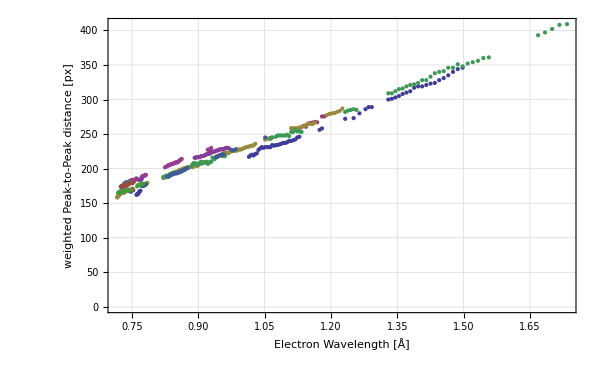

```mathematica
ListPlot[allpeaks,FrameLabel->{StyleForm["Electron Wavelength [Å]",FontSize->14],StyleForm["weighted Peak-to-Peak distance [px]",FontSize->14]},niceStyle]
```

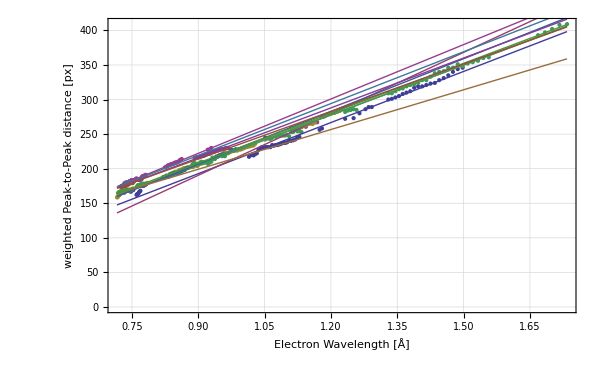

```mathematica
GroupPeakFitPlot[allpeaks,allfits1,"","Electron Wavelength [Å]","weighted Peak-to-Peak distance [px]"]
```

```mathematica
Manipulate[TableForm[{allfits1⟦m⟧[{"ParameterTable","RSquared"}],PeakFitPlot[allpeaks⟦m⟧,allfits1⟦m⟧,"","",""]}],{m,1,Length[allfits1],1}]
```

```mathematica
allfits1average={1/Length[allfits1] Sum[(m/.allfits1⟦i⟧["BestFitParameters"]),{i,1,Length[allfits1]}],1/Length[allfits1] √Sum[(allfits1⟦i⟧["ParameterErrors"]⟦1⟧)^2,{i,1,Length[allfits1]}],1/Length[allfits1] Sum[(n/.allfits1⟦i⟧["BestFitParameters"]),{i,1,Length[allfits1]}],1/Length[allfits1] √Sum[(allfits1⟦i⟧["ParameterErrors"]⟦2⟧)^2,{i,1,Length[allfits1]}]}
```

{244.541,4.68505,-12.8316,4.09592}

```mathematica
ErrorForm[{(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits1average⟦1⟧,(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits1average⟦1⟧√((allfits1average⟦2⟧/allfits1average⟦1⟧)^2+((calibfit3["ParameterErrors"]⟦1⟧)/(A/.calibfit3["BestFitParameters"]))^2)},3]
```

2.314 ± 0.196

```mathematica
ErrorForm[{√2*(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits1average⟦1⟧,√2*(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits1average⟦1⟧√((allfits1average⟦2⟧/allfits1average⟦1⟧)^2+((calibfit3["ParameterErrors"]⟦1⟧)/(A/.calibfit3["BestFitParameters"]))^2)},3]
```

3.272 ± 0.277

#### Linear Fit with forced zero intercept

```mathematica
allfits2=NonlinearModelFit[#,m*x,{m},x]&/@allpeaks;
```

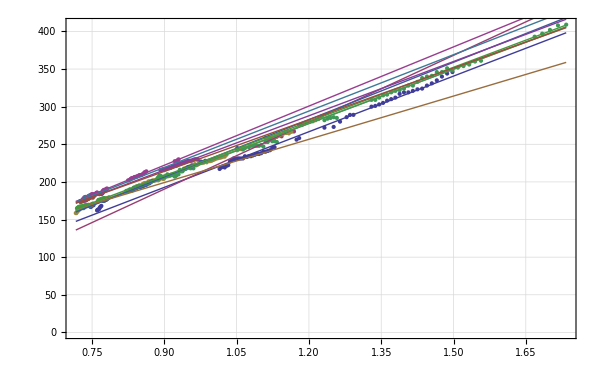

```mathematica
GroupPeakFitPlot[allpeaks,allfits1]
```

```mathematica
Manipulate[TableForm[{allfits2⟦m⟧[{"ParameterTable","RSquared"}],PeakFitPlot[allpeaks⟦m⟧,allfits2⟦m⟧,"","",""]}],{m,1,Length[allfits2],1}]
```

```mathematica
allfits2average={1/Length[allfits2] Sum[(m/.allfits2⟦i⟧["BestFitParameters"]),{i,1,Length[allfits2]}],1/Length[allfits2] √Sum[(allfits2⟦i⟧["ParameterErrors"]⟦1⟧)^2,{i,1,Length[allfits2]}]}
```

{233.265,0.0992858}

```mathematica
ErrorForm[{(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits2average⟦1⟧,(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits2average⟦1⟧√((allfits2average⟦2⟧/allfits2average⟦1⟧)^2+((calibfit3["ParameterErrors"]⟦1⟧)/(A/.calibfit3["BestFitParameters"]))^2)},3]
```

2.426 ± 0.200

```mathematica
ErrorForm[{(√2*2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits2average⟦1⟧,√2*(2*Abs[(A/.calibfit3["BestFitParameters"])])/allfits2average⟦1⟧√((allfits2average⟦2⟧/allfits2average⟦1⟧)^2+((calibfit3["ParameterErrors"]⟦1⟧)/(A/.calibfit3["BestFitParameters"]))^2)},3]
```

3.431 ± 0.283

#### Cherrypicking

```mathematica
cherries={peak10,peak11b,peak01,peak20,peak02,peak21b,peak12b,peak22b};
```

```mathematica
cherryfits=NonlinearModelFit[#,m*x,{m},x]&/@cherries;
```

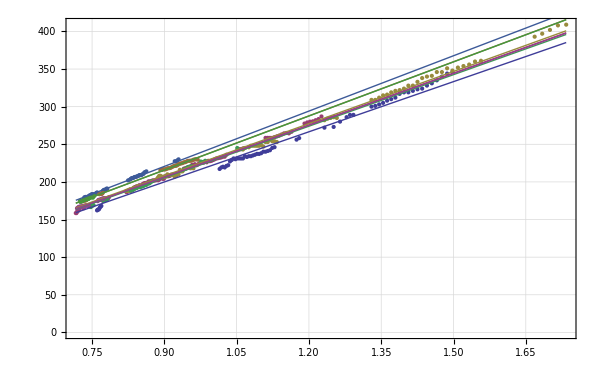

```mathematica
GroupPeakFitPlot[cherries,cherryfits]
```

```mathematica
Manipulate[TableForm[{allfits2⟦m⟧["ParameterTable"],PeakFitPlot[cherries⟦m⟧,cherryfits⟦m⟧,"","",""]}],{m,1,Length[cherryfits],1}]
```

```mathematica
cherryfitsaverage={1/Length[cherryfits] Sum[(m/.cherryfits⟦i⟧["BestFitParameters"]),{i,1,Length[cherryfits]}],1/Length[cherryfits] √Sum[(cherryfits⟦i⟧["ParameterErrors"]⟦1⟧)^2,{i,1,Length[cherryfits]}]}
```

{233.177,0.113963}

```mathematica
ErrorForm[{(2*Abs[(A/.calibfit2["BestFitParameters"])])/cherryfitsaverage⟦1⟧,(2*Abs[(A/.calibfit2["BestFitParameters"])])/cherryfitsaverage⟦1⟧√((cherryfitsaverage⟦2⟧/cherryfitsaverage⟦1⟧)^2+((calibfit2["ParameterErrors"]⟦1⟧)/(A/.calibfit2["BestFitParameters"]))^2)},3]
```

2.427 ± 0.144

### Perpendicular Lattice Constant

```mathematica
ivpeakfitsall={IvPeakFit[ivdata,{85,100}],IvPeakFit[ivdata,{110,140}],IvPeakFit[ivdata,{140,190}],IvPeakFit[ivdata,{140,160}],IvPeakFit[ivdata,{160,190}],IvPeakFit[ivdata,{185,240}],IvPeakFit[ivdata,{185,200}],IvPeakFit[ivdata,{205,240}],IvPeakFit[ivdata,{240,300}],IvPeakFit[ivdata,{360,440}],IvPeakFit[ivdata,{500,590}]};
```

```mathematica
ivpeakfits={IvPeakFit[ivdata,{85,100}],IvPeakFit[ivdata,{110,140}],IvPeakFit[ivdata,{140,190}],IvPeakFit[ivdata,{185,240}],IvPeakFit[ivdata,{240,300}],IvPeakFit[ivdata,{360,440}],IvPeakFit[ivdata,{500,590}]};
```

```mathematica
ivpeakfitsside={IvPeakFit[ivdata,{140,160}],IvPeakFit[ivdata,{160,190}],IvPeakFit[ivdata,{185,200}],IvPeakFit[ivdata,{205,240}]};
```

```mathematica
peak1=IvPeakFit[ivdata,{85,100}];
```

```mathematica
peak2=IvPeakFit[ivdata,{110,140}];
```

```mathematica
peak3=IvPeakFit[ivdata,{140,190}];
```

```mathematica
peak3a=IvPeakFit[ivdata,{140,160}];
```

```mathematica
peak3b=IvPeakFit[ivdata,{160,190}];
```

```mathematica
peak3both=IvPeakFit2[ivdata,{140,160,190}];
```

```mathematica
peak4=IvPeakFit[ivdata,{185,240}];
```

```mathematica
peak4a=IvPeakFit[ivdata,{185,200}];
```

```mathematica
peak4b=IvPeakFit[ivdata,{205,240}];
```

```mathematica
peak4both=IvPeakFit2[ivdata,{185,202,240}];
```

```mathematica
peak5=IvPeakFit[ivdata,{240,300}];
```

```mathematica
peak6=IvPeakFit[ivdata,{360,440}];
```

```mathematica
peak7=IvPeakFit[ivdata,{500,590}];
```

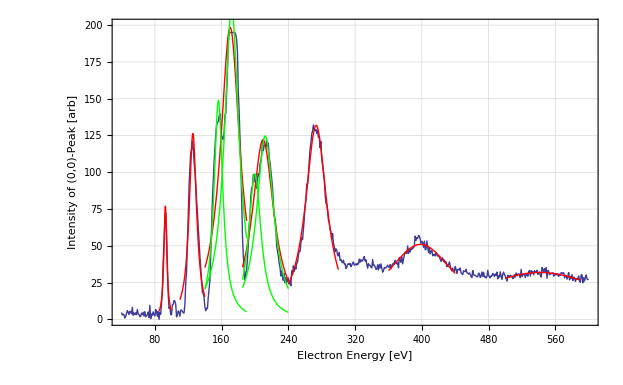

```mathematica
Show[ListPlot[ivdata,Joined->True,PlotRange->{0,200}],Plot[Normal[peak1],{x,85,100},PlotStyle->Red],Plot[Normal[peak2],{x,110,140},PlotStyle->Red],Plot[Normal[peak3],{x,140,190},PlotStyle->Red],Plot[{Normal[peak3a],Normal[peak3b]},{x,140,190},PlotStyle->Green],Plot[Normal[peak4],{x,185,240},PlotStyle->Red],Plot[{Normal[peak4a],Normal[peak4b]},{x,185,240},PlotStyle->Green],Plot[Normal[peak5],{x,240,300},PlotStyle->Red],Plot[Normal[peak6],{x,360,440},PlotStyle->Red],Plot[Normal[peak7],{x,500,590},PlotStyle->Red],niceStyle,FrameLabel->{StyleForm["Electron Energy [eV]",FontSize->14],StyleForm["Intensity of (0,0)-Peak [arb]",FontSize->14]}]
```

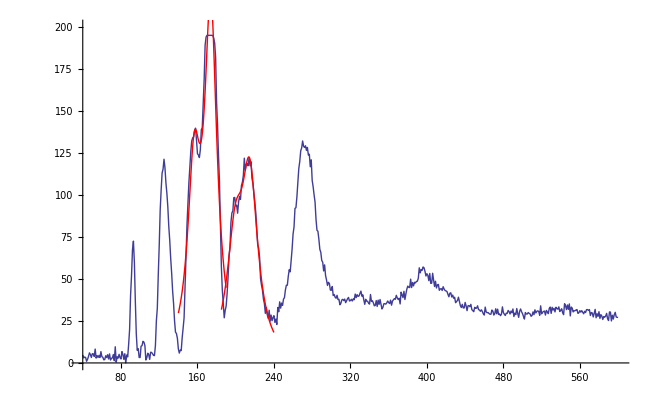

```mathematica
Show[ListPlot[ivdata,Joined->True,PlotRange->{0,200}],Plot[Normal[peak3both],{x,140,190},PlotStyle->Red],Plot[Normal[peak4both],{x,185,240},PlotStyle->Red]]
```

```mathematica
Manipulate[ivpeakfitsall⟦i⟧["ParameterTable"],{i,1,Length[ivpeakfitsall],1}]
```

```mathematica
Manipulate[ivpeakfits⟦i⟧["ParameterTable"],{i,1,Length[ivpeakfits],1}]
```

```mathematica
Manipulate[ivpeakfitsside⟦i⟧["ParameterTable"],{i,1,Length[ivpeakfitsside],1}]
```

```mathematica
ivfitsparasall={(a/.#)&/@(#["BestFitParameters"]&/@ivpeakfitsall),(#["ParameterErrors"]⟦2⟧&/@ivpeakfitsall)}ᵀ;
```

```mathematica
ivfitsparas={(a/.#)&/@(#["BestFitParameters"]&/@ivpeakfits),(#["ParameterErrors"]⟦2⟧&/@ivpeakfits)}ᵀ;
```

```mathematica
ivfitsparasside={(a/.#)&/@(#["BestFitParameters"]&/@ivpeakfitsside),(#["ParameterErrors"]⟦2⟧&/@ivpeakfitsside)}ᵀ;
```

```mathematica
peaksforfit={ivfitsparasside⟦2⟧,ivfitsparas⟦5⟧,ivfitsparas⟦6⟧,ivfitsparas⟦7⟧}ᵀ
```

{{172.038,273.294,398.389,541.573},{0.39149,0.157523,0.564373,1.39946}}

```mathematica
Manipulate[
plotfit=NonlinearModelFit[{Table[i^2,{i,a,(a+3)}],peaksforfit⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit⟦2⟧^-2,
VarianceEstimatorFunction->(1&)];
TableForm[{plotfit[{"ParameterTable","RSquared"}],Show[ErrorListPlot[Prepend[peaksforfit,Table[i^2,{i,a,(a+3)}]]ᵀ,FrameLabel->{StyleForm["Squared Peak order [1]",FontSize->14],StyleForm["Electron Energy [eV]",FontSize->14]}],Plot[Normal[plotfit],{x,(a^2-1),(Evaluate[(a+3)^2]+1)}],niceStyle,PlotLabel->Style[" ",20]]}],
{a,1,10,1}]
```

```mathematica
finalplotfit=NonlinearModelFit[{Table[i^2,{i,4,7,1}],peaksforfit⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit⟦2⟧^-2,
VarianceEstimatorFunction->(1&)]
```

FittedModel[-8.43763+11.2721 x]

```mathematica
ErrorForm[{12.26/(2*√(m/.finalplotfit["BestFitParameters"])),√(12.26/(4*(m/.finalplotfit["BestFitParameters"])^(3/2))*finalplotfit["ParameterErrors"]⟦1⟧)^2},3]
```

1.826 ± 0.003

```mathematica
peaksforfit1={ivfitsparas⟦3⟧,ivfitsparas⟦5⟧,ivfitsparas⟦6⟧,ivfitsparas⟦7⟧}ᵀ;
```

```mathematica
Manipulate[
plotfit=NonlinearModelFit[{Table[i^2,{i,a,(a+3)}],peaksforfit1⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit1⟦2⟧^-2,
VarianceEstimatorFunction->(1&)];
TableForm[{plotfit[{"ParameterTable","RSquared"}],Show[ErrorListPlot[Prepend[peaksforfit1,Table[i^2,{i,a,(a+3)}]]ᵀ,FrameLabel->{StyleForm["Squared Peak order [1]",FontSize->14],StyleForm["Electron Energy [eV]",FontSize->14]}],Plot[Normal[plotfit],{x,(a^2-1),(Evaluate[(a+3)^2]+1)}],niceStyle,PlotLabel->Style[" ",20]]}],
{a,1,10,1}]
```

```mathematica
finalplotfit1=NonlinearModelFit[{Table[i^2,{i,4,7,1}],peaksforfit1⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit⟦2⟧^-2,
VarianceEstimatorFunction->(1&)]
```

FittedModel[-10.756+11.3565 x]

```mathematica
ErrorForm[{12.26/(2*√(m/.finalplotfit1["BestFitParameters"])),√(12.26/(4*(m/.finalplotfit1["BestFitParameters"])^(3/2))*finalplotfit1["ParameterErrors"]⟦1⟧)^2},3]
```

1.819 ± 0.003

```mathematica
finalplotfit2=NonlinearModelFit[{Table[i^2,{i,5,8,1}],peaksforfit1⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit⟦2⟧^-2,
VarianceEstimatorFunction->(1&)]
```

FittedModel[-68.3337+9.49832 x]

```mathematica
ErrorForm[{12.26/(2*√(m/.finalplotfit2["BestFitParameters"])),√(12.26/(4*(m/.finalplotfit2["BestFitParameters"])^(3/2))*finalplotfit2["ParameterErrors"]⟦1⟧)^2},3]
```

1.989 ± 0.003

```mathematica
peaksforfit2={{(a2/.peak3both["BestFitParameters"]),peak3both["ParameterErrors"]⟦3⟧},ivfitsparas⟦5⟧,ivfitsparas⟦6⟧,ivfitsparas⟦7⟧}ᵀ
```

{{173.931,273.294,398.389,541.573},{0.657784,0.157523,0.564373,1.39946}}

```mathematica
Manipulate[
plotfit=NonlinearModelFit[{Table[i^2,{i,a,(a+3)}],peaksforfit2⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit2⟦2⟧^-2,
VarianceEstimatorFunction->(1&)];
TableForm[{plotfit[{"ParameterTable","RSquared"}],Show[ErrorListPlot[Prepend[peaksforfit2,Table[i^2,{i,a,(a+3)}]]ᵀ,FrameLabel->{StyleForm["Squared Peak order [1]",FontSize->14],StyleForm["Electron Energy [eV]",FontSize->14]}],Plot[Normal[plotfit],{x,(a^2-1),(Evaluate[(a+3)^2]+1)}],niceStyle,PlotLabel->Style[" ",20]]}],
{a,1,10,1}]
```

```mathematica
finalplotfit3=NonlinearModelFit[{Table[i^2,{i,4,7,1}],peaksforfit2⟦1⟧}ᵀ,m*x+n,{m,n},x,
Weights->peaksforfit2⟦2⟧^-2,
VarianceEstimatorFunction->(1&)]
```

FittedModel[-7.24058+11.2285 x]

```mathematica
ErrorForm[{12.26/(2*√(m/.finalplotfit3["BestFitParameters"])),√(12.26/(4*(m/.finalplotfit3["BestFitParameters"])^(3/2))*finalplotfit3["ParameterErrors"]⟦1⟧)^2},3]
```

1.829 ± 0.003

## Playarea

```mathematica
Export["grid1.pdf",GraphicsGrid[{{PeakFitPlot[allpeaks⟦1⟧,allfits1⟦1⟧,"Peaks (1,0) and (-1,0)"],PeakFitPlot[allpeaks⟦2⟧,allfits1⟦2⟧,"Peaks (1,1) and (-1,-1)"]},{PeakFitPlot[allpeaks⟦3⟧,allfits1⟦3⟧,"Peaks (1,-1) and (-1,1)"],PeakFitPlot[allpeaks⟦4⟧,allfits1⟦4⟧,"Peaks (0,1) and (0,-1)"]},{PeakFitPlot[allpeaks⟦5⟧,allfits1⟦5⟧,"Peaks (2,0) and (-2,0)"],PeakFitPlot[allpeaks⟦6⟧,allfits1⟦6⟧,"Peaks (0,2) and (0,-2)"]}}]]
```

grid1.pdf

```mathematica
Export["grid2.pdf",GraphicsGrid[{{PeakFitPlot[allpeaks⟦7⟧,allfits1⟦7⟧,"Peaks (2,1) and (-2,-1)"],PeakFitPlot[allpeaks⟦8⟧,allfits1⟦8⟧,"Peaks (2,-1) and (-2,1)"]},{PeakFitPlot[allpeaks⟦9⟧,allfits1⟦9⟧,"Peaks (1,2) and (-1,-2)"],PeakFitPlot[allpeaks⟦10⟧,allfits1⟦10⟧,"Peaks (1,-2) and (-1,2)"]},{PeakFitPlot[allpeaks⟦11⟧,allfits1⟦11⟧,"Peaks (2,-2) and (-2,2)"]}}]]
```

grid2.pdf

Manipulate[

peakdata=Select[ivdata,First[#]≥min&& First[#]≤max&];
peakfit=NonlinearModelFit[peakdata,A/(1+((x-a)/b)^2),{{A,Round},{a,},b},x,MaxIterations→1000];
Column[
Show[
ListPlot[ivdata,Joined→True,PlotRange→{0,200}],Plot[Normal[peakfit],{x,240,300}],

]
],
{min,Min[First[#]&/@ivdata],Max[First[#]&/@ivdata]-1},{max,min+1,Max[First[#]&/@ivdata]}]